```mathematica
U[ψ_,h_,ξ_,λ_,β_]:=9λ Sinh[h/(√6)]^4+1/(4β)(1-E^(-√(2/3)ψ)Cosh[h/(√6)]^2-6ξ Sinh[h/(√6)]^2)^2;
U1[ψ_,h_,ξ_,λ_,β_]:=D[U[ψ,h,ξ,λ,β],ψ];
U2[ψ_,h_,ξ_,λ_,β_]:=D[U[ψ,h,ξ,λ,β],h];
U11[ψ_,h_,ξ_,λ_,β_]:=D[U[ψ,h,ξ,λ,β],{ψ,2}];
U22[ψ_,h_,ξ_,λ_,β_]:=D[U[ψ,h,ξ,λ,β],{h,2}];
U12[ψ_,h_,ξ_,λ_,β_]:=D[D[U[ψ,h,ξ,λ,β],ψ],h];
Mm[ξ_]:=(1.3*10^-5)/(√(1-5.07*10^-8*ξ^2));(*Observational constraint for M and ξ*)
β[ξ_]:=1/(3 Mm[ξ]^2);
H0=4.05998*10^-6;
hini[ψ_,ξ_]:=(5.07*^-8 (-1+ⅇ^(√(2/3) ψ)) ξ)^(1/2)+0.000001;(*Initial condition for Higgs*)
nhini[ψ_,ξ_]:=√6 ArcSinh[hini[ψ,ξ]/(√6)E^(-ψ/(√6))];(*intitial condition for new heavy field*)
Φini[ψ_,ξ_]:=√6 Log[E^(ψ/(√6))Cosh[nhini[ψ,ξ]/(√6)]];(*initial condition for new light field*)
m112[t_,ξ_,λ_]:=U11[Φ[t],nh[t],ξ,λ,β[ξ]]-10^-4 3/2 H'[t]-9/4 H[t]^2;
m222[t_,ξ_,λ_]:=U22[Φ[t],nh[t],ξ,λ,β[ξ]]-10^-4 3/2 H'[t]-9/4 H[t]^2;
mh2[t_,ξ_,λ_]:=1/2(m222[t,ξ,λ]+m112[t,ξ,λ])(1+(1-4((m112[t,ξ,λ]m222[t,ξ,λ]-U12[Φ[t],nh[t],ξ,λ,β[ξ]]^2)/(m222[t,ξ,λ]+m112[t,ξ,λ])^2))^(1/2));
ml2[t_,ξ_,λ_]:=1/2(m222[t,ξ,λ]+m112[t,ξ,λ])(1-(1-4((m112[t,ξ,λ]m222[t,ξ,λ]-U12[Φ[t],nh[t],ξ,λ,β[ξ]]^2)/(m222[t,ξ,λ]+m112[t,ξ,λ])^2))^(1/2));
(*mh2[t_,ξ_,λ_]:=1/2(U22[Φ[t],nh[t],ξ,λ,β[ξ]]+U11[Φ[t],nh[t],ξ,λ,β[ξ]])(1+(1-4((U11[Φ[t],nh[t],ξ,λ,β[ξ]]U22[Φ[t],nh[t],ξ,λ,β[ξ]]-U12[Φ[t],nh[t],ξ,λ,β[ξ]]^2)/(U22[Φ[t],nh[t],ξ,λ,β[ξ]]+U11[Φ[t],nh[t],ξ,λ,β[ξ]])^2))^(1/2));*)(*the effective mass of the heavy mode after field rotation*)(*This is approximation because we do not have so clean ω for δϕ and δh*)
ωh2[t_,k_,ξ_,λ_]:=k^2 a[t]^-2+mh2[t,ξ,λ];
ωl2[t_,k_,ξ_,λ_]:=k^2 a[t]^-2+ml2[t,ξ,λ];
tan2theta[t_,ξ_,λ_]:=2U12[Φ[t],nh[t],ξ,λ,β[ξ]]/(U11[Φ[t],nh[t],ξ,λ,β[ξ]]-U22[Φ[t],nh[t],ξ,λ,β[ξ]]);
costheta[t_,ξ_,λ_]:=1/(√2)√(tan2theta[t,ξ,λ]^2/(1+tan2theta[t,ξ,λ]^2-tan2theta[t,ξ,λ] √(1+tan2theta[t,ξ,λ]^-2)));
sintheta[t_,ξ_,λ_]:=(-1/tan2theta[t,ξ,λ]+√(1+tan2theta[t,ξ,λ]^-2))1/(√2)√(tan2theta[t,ξ,λ]^2/(1+tan2theta[t,ξ,λ]^2-tan2theta[t,ξ,λ] √(1+tan2theta[t,ξ,λ]^-2)));
m112ini[ψ_,ξ_,λ_]:=1/(3 β[ξ])ⅇ^(-2 √(2/3) Φini[ψ,ξ]) (2 Cosh[nhini[ψ,ξ]/(√6)]^4+ⅇ^(√(2/3) Φini[ψ,ξ]) Cosh[nhini[ψ,ξ]/(√6)]^2 (-1+6 ξ Sinh[nhini[ψ,ξ]/(√6)]^2))-9/4 H0^2;
m222ini[ψ_,ξ_,λ_]:=1/(12 β[ξ])ⅇ^(-2 √(2/3) Φini[ψ,ξ]) (-(-1+2 ⅇ^(√(2/3) Φini[ψ,ξ])+12 ⅇ^(2 √(2/3) Φini[ψ,ξ]) (3 β[ξ] λ+ξ+3 ξ^2)) Cosh[√(2/3) nhini[ψ,ξ]]+(1+12 ⅇ^(√(2/3) Φini[ψ,ξ]) ξ+36 ⅇ^(2 √(2/3) Φini[ψ,ξ]) (β[ξ] λ+ξ^2)) Cosh[2 √(2/3) nhini[ψ,ξ]])-9/4 H0^2;
mh2ini[ψ_,ξ_,λ_]:=1/2(m222ini[ψ,ξ,λ]+m112ini[ψ,ξ,λ])(1+(1-4((m112ini[ψ,ξ,λ]m222ini[ψ,ξ,λ]-(-1/(6 β[ξ])ⅇ^(-2 √(2/3) Φini[ψ,ξ]) (1-ⅇ^(√(2/3) Φini[ψ,ξ])+(1+6 ⅇ^(√(2/3) Φini[ψ,ξ]) ξ) Cosh[√(2/3) nhini[ψ,ξ]]) Sinh[√(2/3) nhini[ψ,ξ]])^2)/(m222ini[ψ,ξ,λ]+m112ini[ψ,ξ,λ])^2))^(1/2));
ml2ini[ψ_,ξ_,λ_]:=1/2(m222ini[ψ,ξ,λ]+m112ini[ψ,ξ,λ])(1-(1-4((m112ini[ψ,ξ,λ]m222ini[ψ,ξ,λ]-(-1/(6 β[ξ])ⅇ^(-2 √(2/3) Φini[ψ,ξ]) (1-ⅇ^(√(2/3) Φini[ψ,ξ])+(1+6 ⅇ^(√(2/3) Φini[ψ,ξ]) ξ) Cosh[√(2/3) nhini[ψ,ξ]]) Sinh[√(2/3) nhini[ψ,ξ]])^2)/(m222ini[ψ,ξ,λ]+m112ini[ψ,ξ,λ])^2))^(1/2));
ωh2ini[k_,ψ_,ξ_,λ_]:=k^2+mh2ini[ψ,ξ,λ];
ωl2ini[k_,ψ_,ξ_,λ_]:=k^2+ml2ini[ψ,ξ,λ];
(*ωH2ini[k_,ψ_,ξ_,λ_]:=k^2+1/(12 β[ξ])ⅇ^(-2 √(2/3) Φini[ψ,ξ]) (-(-1+2 ⅇ^(√(2/3) Φini[ψ,ξ])+12 ⅇ^(2 √(2/3) Φini[ψ,ξ]) (3 β[ξ] λ+ξ+3 ξ^2)) Cosh[√(2/3) nhini[ψ,ξ]]+(1+12 ⅇ^(√(2/3) Φini[ψ,ξ]) ξ+36 ⅇ^(2 √(2/3) Φini[ψ,ξ]) (β[ξ] λ+ξ^2)) Cosh[2 √(2/3) nhini[ψ,ξ]])-9/4 H0^2;
ωL2ini[k_,ψ_,ξ_,λ_]:=k^2+(ⅇ^(-2 √(2/3) Φini[ψ,ξ]) (2 Cosh[nhini[ψ,ξ]/(√6)]^4+ⅇ^(√(2/3) Φini[ψ,ξ]) Cosh[nhini[ψ,ξ]/(√6)]^2 (-1+6 ξ Sinh[nhini[ψ,ξ]/(√6)]^2)))/(3 β[ξ])-9/4 H0^2;*)
mT[t_,g_]:=g/2 nh[t] ;(*mass of transverse mode*)
ωlg2[t_,k_,g_]:=k^2 a[t]^-2+mT[t,g]^2-k^2/(k^2+a[t]^2 mT[t,g]^2)(10^-4 H'[t]+2 H[t]^2+10^-4*3H[t] nh'[t]/nh[t]+10^-8 nh''[t]/nh[t]-3((10^-4 g/2 nh'[t]+H[t]mT[t,g])^2)/(k^2 a[t]^-2+mT[t,g]^2));(*ω^2 of the longitudinal mode of the gauge field*)
mTini[g_,ψ_,ξ_]:=g/2 nhini[ψ,ξ];
ωlg2ini[k_,g_,ψ_,ξ_,λ_]:=k^2+mTini[g,ψ,ξ]^2-k^2/(k^2+mTini[g,ψ,ξ]^2)(2 H0^2-nhini[ψ,ξ]^-1(1/(√6 β[ξ])ⅇ^(-2 √(2/3) Φini[ψ,ξ]) Cosh[nhini[ψ,ξ]/(√6)] Sinh[nhini[ψ,ξ]/(√6)] ((1+6 ⅇ^(√(2/3) Φini[ψ,ξ]) ξ) Cosh[nhini[ψ,ξ]/(√6)]^2+ⅇ^(√(2/3) Φini[ψ,ξ]) (-1-6 ⅇ^(√(2/3) Φini[ψ,ξ]) ξ+6 (ξ+6 ⅇ^(√(2/3) Φini[ψ,ξ]) (β[ξ] λ+ξ^2)) Sinh[nhini[ψ,ξ]/(√6)]^2)))-3(H0*mTini[g,ψ,ξ])^2/(k^2+mTini[g,ψ,ξ]^2));
(*tan2thetaini[ψ_,h_,ξ_,λ_]:=2U12[ψ,h,ξ,λ,β[ξ]]/(U11[ψ,h,ξ,λ,β[ξ]]-U22[ψ,h,ξ,λ,β[ξ]]);
costhetaini[ψ_,h_,ξ_,λ_]:=1/(√2)√(tan2thetaini[ψ,h,ξ,λ]^2/(1+tan2thetaini[ψ,h,ξ,λ]^2-tan2thetaini[ψ,h,ξ,λ] √(1+tan2thetaini[ψ,h,ξ,λ]^-2)));
sinthetaini[ψ_,h_,ξ_,λ_]:=(-1/tan2thetaini[ψ,h,ξ,λ]+√(1+tan2thetaini[ψ,h,ξ,λ]^-2))1/(√2)√(tan2thetaini[ψ,h,ξ,λ]^2/(1+tan2thetaini[ψ,h,ξ,λ]^2-tan2thetaini[ψ,h,ξ,λ] √(1+tan2thetaini[ψ,h,ξ,λ]^-2)));*)
(*parspe[t_,k_,ξ_,λ_]:=;*)
solbgfb[ξ_,λ_,ψ0_,Tend_]:=NDSolve[{10^-2 Φ''[Tt]+10^2*3H[Tt]Φ'[Tt]+10^-2 √(2/3)nh'[Tt]Tanh[nh[Tt]/(√6)]Φ'[Tt]+10^6 U1[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]/Cosh[nh[Tt]/(√6)]^2==0,
10^-2 nh''[Tt]+10^2*3H[Tt]nh'[Tt]+10^6 U2[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]-10^-2 1/(2 √6)Φ'[Tt]^2 Sinh[√(2/3)nh[Tt]]==0,
-2*10^2*H'[Tt]==10^-2*(Φ'[Tt]^2 Cosh[nh[Tt]/(√6)]^2+nh'[Tt]^2),
a'[Tt]==10^4 a[Tt]H[Tt],
Φ[0]==Φini[ψ0,ξ],
Φ'[0]==0,
nh[0]==nhini[ψ0,ξ],
nh'[0]==0,
a[0]==1,
H[0]==H0},
{Φ,nh,H,a},{Tt,0,Tend}, 
Method->{"ImplicitRungeKutta","DifferenceOrder"->10,"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->0.9}},MaxSteps->10000000];(*This function only solves background. It can be used for the case where we only need background solution*)
solfofb[k_,g_,ξ_,λ_,ψ0_,Tend_]:=NDSolve[{10^-2 Φ''[Tt]+10^2*3H[Tt]Φ'[Tt]+10^-2 √(2/3)nh'[Tt]Tanh[nh[Tt]/(√6)]Φ'[Tt]+10^6 U1[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]/Cosh[nh[Tt]/(√6)]^2==0,
10^-2 nh''[Tt]+10^2*3H[Tt]nh'[Tt]+10^6 U2[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]-10^-2 1/(2 √6)Φ'[Tt]^2 Sinh[√(2/3)nh[Tt]]==0,
-2*10^2*H'[Tt]==10^-2*(Φ'[Tt]^2 Cosh[nh[Tt]/(√6)]^2+nh'[Tt]^2),
a'[Tt]==10^4 a[Tt]H[Tt],
10^-2 dnhR''[Tt]+10^6*k^2/a[Tt]^2 dnhR[Tt]+10^6*U12[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]dΦR[Tt]+(10^6*U22[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]-10^2*3/2 H'[Tt]-10^6*9/4 H[Tt]^2)dnhR[Tt]==0,
10^-2 dnhI''[Tt]+10^6*k^2/a[Tt]^2 dnhI[Tt]+10^6*U12[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]dΦI[Tt]+(10^6*U22[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]-10^2*3/2 H'[Tt]-10^6*9/4 H[Tt]^2)dnhI[Tt]==0,
10^-2 dΦR''[Tt]+10^6*k^2/a[Tt]^2 dΦR[Tt]+(10^6*U11[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]-10^2*3/2 H'[Tt]-10^6*9/4 H[Tt]^2)dΦR[Tt]+10^6*U12[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]dnhR[Tt]==0,
10^-2 dΦI''[Tt]+10^6*k^2/a[Tt]^2 dΦI[Tt]+(10^6*U11[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]-10^2*3/2 H'[Tt]-10^6*9/4 H[Tt]^2)dΦI[Tt]+10^6*U12[Φ[Tt],nh[Tt],ξ,λ,β[ξ]]dnhI[Tt]==0,
10^-2 dWR''[Tt]+10^2 H[Tt]dWR'[Tt]+10^6*ωlg2[Tt,k,g]dWR[Tt]==0,
10^-2 dWI''[Tt]+10^2 H[Tt]dWI'[Tt]+10^6*ωlg2[Tt,k,g]dWI[Tt]==0,
Φ[0]==Φini[ψ0,ξ],
Φ'[0]==0,
nh[0]==nhini[ψ0,ξ],
nh'[0]==0,
a[0]==1,
H[0]==H0,
dΦR[0]==1/(√2)ωl2ini[k,ψ0,ξ,λ]^(-1/4),
dΦR'[0]==0,
dΦI[0]==0,
dΦI'[0]==-10^4/(√2)ωl2ini[k,ψ0,ξ,λ]^(1/4),
dnhR[0]==1/(√2)ωh2ini[k,ψ0,ξ,λ]^(-1/4),
dnhR'[0]==0,
dnhI[0]==0,
dnhI'[0]==-10^4/(√2)ωh2ini[k,ψ0,ξ,λ]^(1/4) ,
dWR[0]==1/(√2)ωlg2ini[k,g,ψ0,ξ,λ]^(-1/4),
dWR'[0]==0,
dWI[0]==0,
dWI'[0]==-10^4/(√2)ωlg2ini[k,g,ψ0,ξ,λ]^(1/4)},
{Φ,nh,H,a,dΦR,dΦI,dnhR,dnhI,dWR,dWI},{Tt,0,Tend}, 
Method->{"ImplicitRungeKutta","DifferenceOrder"->10,"ImplicitSolver"->{"Newton", AccuracyGoal->MachinePrecision, PrecisionGoal->MachinePrecision,"IterationSafetyFactor"->0.9,MaxIterations->50}},MaxSteps->10000000];(*Here, the inhomogeneities of H and Φ have been rescaled by a^(3/2) which correspond to H̃ and Φ̃ in Bezrukov et al.*)
heavynumden[t_,kp_,at_,ξ_,λ_]:=1/2(Abs[(ωh2[t,kp*at,ξ,λ])^(1/4)*((dnhR[t]+I*dnhI[t])costheta[t,ξ,λ]-(dΦR[t]+I*dΦI[t])sintheta[t,ξ,λ])-I*(ωh2[t,kp*at,ξ,λ])^(-1/4)*10^-4((dnhR'[t]+I*dnhI'[t])costheta[t,ξ,λ]+(dnhR[t]+I*dnhI[t])D[costheta[t,ξ,λ],t]-(dΦR'[t]+I*dΦI'[t])sintheta[t,ξ,λ]-(dΦR[t]+I*dΦI[t])D[sintheta[t,ξ,λ],t])])^2;(*number density of Higgs*)
glnumden[t_,kp_,at_,g_]:=1/2(Abs[(ωlg2[t,kp*at,g])^(1/4)*(dWR[t]+I*dWI[t])-I*(ωlg2[t,kp*at,g])^(-1/4)*10^-4(dWR'[t]+I*dWI'[t])])^2;(*number density of longitudinal mode of gauge boson*)
(*gtnumden[t_,kp_,at_,g_]:=1/2(Abs[(ωtg2[t,kp*at,g])^(1/4)*(dWR[t]+I*dWI[t])-I*(ωtg2[t,kp*at,g])^(-1/4)*10^-4(dWR'[t]+I*dWI'[t])])^2;(*number density of transverse mode of gauge boson*)*)
```

```mathematica
tdip=37.24776;
```

```mathematica
at={a[tdip]/.solbgfb[4.43575910480101127*10^3,1/100,1.2,38]}[[1,1]](*the scale factor at the first dip*)
```

3.20974

```mathematica
Monitor[Table[{i,{i^2/(2 π^2)heavynumden[t,i,at,4.43575910480101127*10^3,1/100]/.{t->tdip}/.solfofb[i*at,1,4.43575910480101127*10^3,1/100,1.2,38]}[[1,1]]},{i,5.*10^-6,1.0*10^-2+5.*10^-6,5.*10^-6}],Grid[{{Text[Style["Number density evaluation:", Darker[Blue,0.66]]],ProgressIndicator[i,{5.*10^-6,1.0*10^-2+5.*10^-6}]},{Text[Style["k_p:",Darker[Blue,0.66]]],i}},Alignment->Left,Dividers->Center]];
data=%;
Export["~/Desktop/N10fullpeak.m",data];
N10fp=Import["~/Desktop/N10fullpeak.m"];
```

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at Tt = 36.9523.

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at Tt = 37.6858.

NDSolve::impsitsf: Unable to satisfy the ImplicitSolver tolerance for IterationSafetyFactor at Tt = 37.9713.

General::stop: Further output of NDSolve::impsitsf will be suppressed during this calculation.

NDSolve::maxit: Maximum number of iterations 50 reached at Tt = 37.0079.

NDSolve::maxit: Maximum number of iterations 50 reached at Tt = 36.9589.

NDSolve::maxit: Maximum number of iterations 50 reached at Tt = 37.2265.

General::stop: Further output of NDSolve::maxit will be suppressed during this calculation.

NDSolve::impsagpg: Unable to satisfy the ImplicitSolver tolerances for AccuracyGoal and PrecisionGoal at Tt = 34.8924.

NDSolve::impsagpg: Unable to satisfy the ImplicitSolver tolerances for AccuracyGoal and PrecisionGoal at Tt = 34.8959.

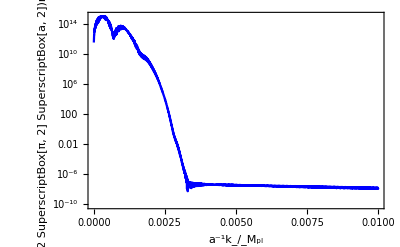

```mathematica
N10fp=Import["~/Desktop/N10fullpeak.m"];
ListLogPlot[N10fp,PlotRange->All,PlotStyle->Blue,Frame->True,FrameLabel->{"a^-1k_/_M_pl","k^2/(2 SuperscriptBox[π, 2] SuperscriptBox[a, 2])n_k_/_M_pl^2"},Joined->True]
```